```mathematica
U[x_]:=a+b*Exp[-x/R]
```

```mathematica
U[x]
```

a+b ⅇ^(-x/R)

```mathematica
U[0]
```

a+b

```mathematica
Umin=U[min]
```

a+b ⅇ^(-min/R)

```mathematica
Umax=U[max]
```

a+b ⅇ^(-max/R)

```mathematica
Solve[Umin==0&&Umax==1,{a,b}]
```

{{a→-ⅇ^(max/R)/(-ⅇ^(max/R)+ⅇ^(min/R)),b→ⅇ^(max/R+min/R)/(-ⅇ^(max/R)+ⅇ^(min/R))}}

```mathematica
{{a->-ⅇ^(max/R)/(-ⅇ^(max/R)+ⅇ^(min/R)),b->ⅇ^(max/R+min/R)/(-ⅇ^(max/R)+ⅇ^(min/R))}}/.{min->20,max->100,R->80}//N
```

{{a→1.58198,b→-2.0313}}

```mathematica
Solve
```

```mathematica
U50=U[50]
```

a+b ⅇ^(-50/R)

```mathematica
NSolve[{U20==0,U100==1,U50==0.5},{a,b,R}]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
solx=Solve[50==60-0.5/R*(0.5*100^2+0.5*20^2-60^2),{R}]
```

{{R→80.}}

```mathematica
0.5*15625/(175-150)
```

312.5

```mathematica
0.5*100^2+0.5*20^2-60^2
```

1600.

```mathematica
U20=U20/.{R->80}
```

a+b/ⅇ^(1/4)

```mathematica
U100=U100/.{R->80}
```

a+b/ⅇ^(5/4)

```mathematica
solx2=Solve[U20==0&&U100==1,{a,b}]//N
```

{{a→1.58198,b→-2.0313}}

```mathematica
0.5*300+0.5*50
```

175.

```mathematica
0.5*300^2+0.5*50^2-175^2
```

15625.

```mathematica
soly=Solve[150==175-0.5/R*(15625),{R}]
```

{{R→312.5}}

```mathematica
soly2=Solve[U[50]==0&&U[300]==1/.sol[[1]],{a,b}]//N
```

{{a→1.81597,b→-2.13106}}

```mathematica
Ux=U[x]/.solx[[1]]/.solx2[[1]]
```

1.58198-2.0313 ⅇ^(-0.0125 x)

```mathematica
Uy=U[y]/.soly[[1]]/.soly2[[1]]
```

1.81597-2.13106 ⅇ^(-0.0032 y)

```mathematica
Uxy[x_,y_]:=
```

```mathematica
Ux/.{x->50}
```

0.494701

```mathematica
r/(r+1)/.{r->1.5}
```

0.6

```mathematica
Uxy[x_,y_]=kx*Ux+ky*Uy+(1-kx-ky)*Ux*Uy
```

(1.58198-2.0313 ⅇ^(-0.0125 x)) kx+(1.58198-2.0313 ⅇ^(-0.0125 x)) (1.81597-2.13106 ⅇ^(-0.0032 y)) (1-kx-ky)+(1.81597-2.13106 ⅇ^(-0.0032 y)) ky

```mathematica
Uxy=Uxy[x,y]/.{kx->0.75,ky->0.6}
```

0.75 (1.58198-2.0313 ⅇ^(-0.0125 x))+0.6 (1.81597-2.13106 ⅇ^(-0.0032 y))-0.35 (1.58198-2.0313 ⅇ^(-0.0125 x)) (1.81597-2.13106 ⅇ^(-0.0032 y))

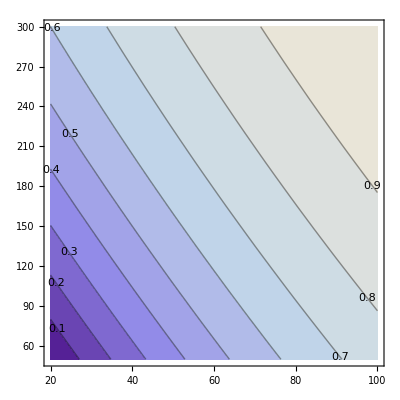

```mathematica
ContourPlot[Uxy,{x,20,100},{y,50,300},ContourLabels->All]
```

```mathematica
U[x_]:=a+b*Exp[-x/R];
```

```mathematica
Ux1=U[x1]/.{a->1.157,b->-0.095,R->200};
```

```mathematica
Ux2=U[x2]/.{a->1.816,b->-1.816,R->1.25};
```

```mathematica
Ux3=U[x3]/.{a->1.027,b->-1.027,R->2.75};
```

```mathematica
U=(((K*k1*Ux1+1)*(K*k2*Ux2+1)*(K*k3*Ux3+1)-1)/K)/.{k1->0.17,k2->0.67,k3->0.83,K->-0.926}
```

-1.07991 (-1+(1-0.15742 (1.157-0.095 ⅇ^(-x1/200))) (1-0.62042 (1.816-1.816 ⅇ^(-0.8 x2))) (1-0.76858 (1.027-1.027 ⅇ^(-0.363636 x3))))

```mathematica
U//Simplify
```

-1.07991 (-1+ⅇ^(-0.005 x1-0.8 x2-0.363636 x3) (0.0149549+0.817865 ⅇ^(x1/200)) (1.12668-0.126683 ⅇ^(0.8 x2)) (0.789332+0.210668 ⅇ^(0.363636 x3)))

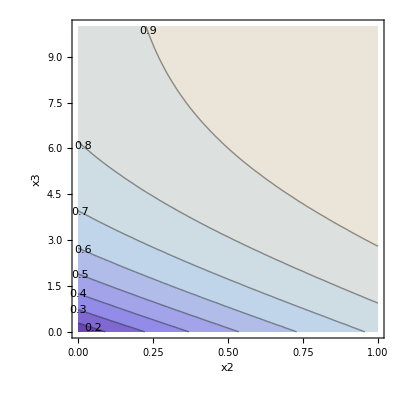

```mathematica
ContourPlot[U/.{x1->-300},{x2,0,1},{x3,0,10},ContourLabels->All,Axes-> True,  AxesLabel->{"x2","x3"}]
```

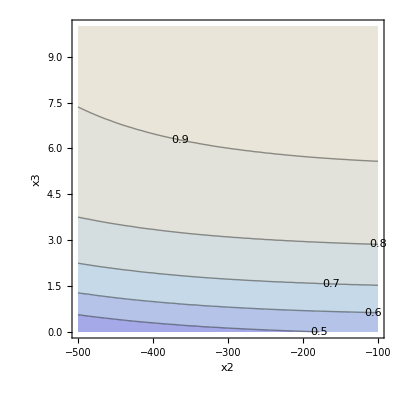

```mathematica
ContourPlot[U/.{x2->0.5},{x1,-500,-100},{x3,0,10},ContourLabels->All,Axes-> True,  AxesLabel->{"x2","x3"}]
```

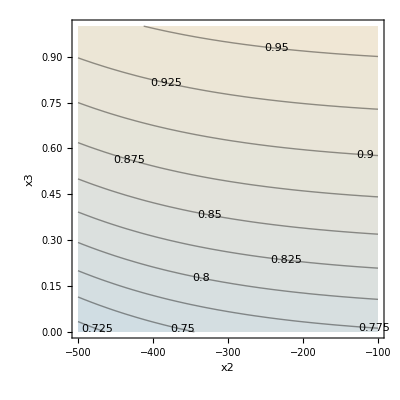

```mathematica
ContourPlot[U/.{x3->5},{x1,-500,-100},{x2,0,1},ContourLabels->All,Axes-> True,  AxesLabel->{"x2","x3"}]
```

```mathematica
Plot3D[U/.{x1->-300},{x2,0,1},{x3,0,10},AxesLabel->{"x2","x3","U(-300,x1,x3)"}]
```

-Graphics3D-